```mathematica
line[phi_, rmax_:5] := Table[Exp[I phi] r, {r,0,rmax, 0.1}]
```

```mathematica
singulPlot = ComplexListPlot[{1}, PlotMarkers->{Automatic, 10},
PlotStyle->{Red}];
```

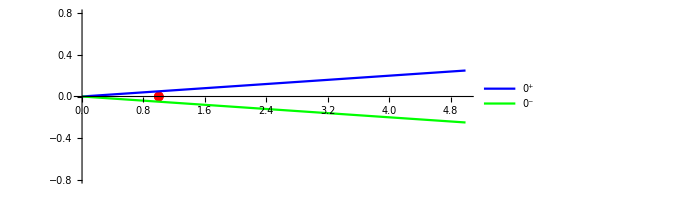

```mathematica
laplaceLinePlus = ComplexListPlot[line[0.05],
Joined->True, PlotStyle->{Blue, 0.4},
PlotLegends->LineLegend[{"0^+"}]];
laplaceLineMinus = ComplexListPlot[line[-0.05],
Joined->True, PlotStyle->{Green, 0.4},
PlotLegends->LineLegend[{"0^-"}]];
plot = Show[singulPlot, laplaceLinePlus, laplaceLineMinus,
PlotRange->{-0.8,0.8}]
```

```mathematica
Export["
```